```mathematica
p[n_,μ_,ψ_]:=1/n 1/(√(2π(ψ+1/n)))Exp[-1/(2(ψ+1/n))(Log[n]-μ)^2];
acc=20;
prec=12;
wp=30;
minrec=10;
maxrec=100;

norm[μ_,ψ_]:=Module[{mid, p1,p2},
mid=Floor[Exp[μ]];
p1=0;
p2=0;
If[mid>1,
p1=NSum[p[n,μ,ψ],{n,1,mid},WorkingPrecision->wp, AccuracyGoal->acc, PrecisionGoal->prec,Method->{NIntegrate,MaxRecursion->maxrec,MinRecursion->minrec}];
p2=NSum[p[n,μ,ψ],{n,mid+1,∞},WorkingPrecision->wp, AccuracyGoal->acc, PrecisionGoal->prec,Method->{NIntegrate,MaxRecursion->maxrec,MinRecursion->minrec}];,
p1=NSum[p[n,μ,ψ],{n,1,∞},WorkingPrecision->wp, AccuracyGoal->acc, PrecisionGoal->prec,Method->{NIntegrate,MaxRecursion->maxrec,MinRecursion->minrec}];
p2=0];
Log[p1+p2]]
```

```mathematica
mumin=-Sqrt[25];
mumax=Sqrt[10];
psimax=1;

Nmu=160;
Npsi=40;
mu=Sign[#]#^2&/@Table[mumin + (mumax-mumin) (i-1)/(Nmu-1) ,{i,1,Nmu}];
psi=#^2&/@Table[(j-1) psimax/(Npsi-1),{j,1,Npsi}];
```

```mathematica
SetSharedVariable[num]
num=0;
Monitor[result=ParallelTable[
Module[{},num++;N[norm[Extract[mu,i],Extract[psi,j]],12]],{i,1,Length[mu]},{j,1,Length[psi]},Method->"FinestGrained"],num]
```

NSum::emcon: Euler-Maclaurin sum failed to converge to requested error tolerance.

{{-313.418938533,-313.213945211,-312.6005796,34,-165.707875857,-161.56045021,-157.515512123},158,{1}}
 |  |  |  |

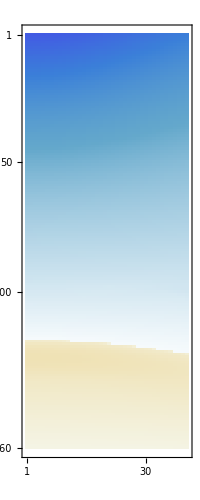

```mathematica
MatrixPlot[result]
```

```mathematica
Export["mu_table.tsv",N[mu,12]]
Export["psi_table.tsv",N[psi,12]]
Export["log_norm_table.tsv",result]
```

mu_table.tsv

psi_table.tsv

log_norm_table.tsv

```mathematica
(* generate test cases *)
mulo = -25;
muhi = 25;
psilo = 0;
psihi = 1.0;

murand = Rationalize[Table[mulo + (muhi - mulo) RandomReal[1],{i,1,5}],10^-12]
psirand =Rationalize[Table[psilo+(psihi-psilo) RandomReal[1],{i,1,5}],10^-12]
normrand =ParallelTable[
N[norm[murand[[i]],psirand[[j]]],12],{i,1,Length[murand]},{j,1,Length[psirand]},Method->"FinestGrained"]
```

{-3091476/154003,17565752/782511,5266501/539761,17463178/1029537,-56907651/2952484}

{403120/760859,536757/1025090,319187/1763413,223937/725727,125268/1035097}

{{-132.836567457,-133.370722005,-171.607050746,-155.027162677,-180.709888717},{1.161468384×10^-10,1.157871771×10^-10,9.755796876×10^-11,1.039831359×10^-10,9.467541922×10^-11},{0.0000377381250187,0.0000376210877616,0.0000316917381709,0.0000337810883095,0.0000307545504235},{2.8018462×10^-8,2.7931699×10^-8,2.353421×10^-8,2.5084171×10^-8,2.283884×10^-8},{-122.552919532,-123.045208201,-158.286065831,-143.004754512,-166.676111059}}

```mathematica
readCounts={1,10,100,1000,10000,100000,1000000,10000000,100000000};
lognormpdf=Table[N[Log[p[readCounts[[k]],murand[[i]],psirand[[j]]]],12]- normrand[[i,j]] ,{k,1,9},{i,1,5},{j,1,5}]
```

{{{0.,0.,0.,0.,0.},{-165.826976262,-166.495438446,-214.341374329,-193.595593167,-225.730883739},{-32.2465932017,-32.3712344664,-41.3072080963,-37.4294149773,-43.437827575},{-95.166981104,-95.547778561,-122.81152649,-110.98839881,-129.30336417},{0.,0.,0.,0.,0.}},{{-267.66066251,-271.07535771,-721.91921978,-460.5160922,-954.49618457},{-325.172485776,-328.372118637,-724.699537888,-499.42780336,-920.55997421},{-47.1058387174,-47.5396837102,-101.463601762,-70.7793365351,-128.178566238},{-173.59670567,-175.28869141,-384.96995795,-265.76899262,-488.62820641},{-250.04220317,-253.22123618,-672.70269919,-429.52652842,-889.01985508}},{{-436.5166644,-442.53429894,-1427.4638302,-805.86765233,-2148.119727},{-300.094481897,-303.516390718,-838.0872992,-504.630196675,-1219.44743552},{-29.8002426402,-30.0802340536,-74.1771253018,-46.6108897736,-105.798775784},{-146.64700524,-148.28523116,-404.41147463,-244.61021818,-587.22324137},{-410.8355439,-416.47698763,-1339.1405852,-756.94700352,-2013.9738328}},{{-560.42287983,-567.99078977,-1835.370731,-1028.0764239,-2809.2596389},{-234.984519227,-237.668181256,-670.409082464,-397.293784577,-996.350191741},{-15.1574059035,-15.2419468439,-29.278492836,-20.3534284649,-40.0429229288},{-102.73135067,-103.85132057,-284.68986746,-170.51760754,-421.01329684},{-530.66337526,-537.79970184,-1731.9049991,-971.43633323,-2649.0949209}},{{-686.13179772,-695.17524018,-2205.2970504,-1243.6716204,-3368.5565863},{-175.150913661,-177.103269366,-493.064836081,-293.39521183,-732.459650602},{-10.0938681174,-10.0913216056,-10.1003042586,-10.0258166199,-10.307901356},{-66.509529345,-67.175158869,-175.17518408,-106.88005943,-257.13579584},{-652.82978686,-661.39887563,-2091.0844072,-1180.8663205,-3191.8959663}},{{-820.84178953,-831.45535476,-2595.9314164,-1473.4876266,-3952.5264228},{-124.955951844,-126.286767125,-341.865261052,-205.593780903,-505.36007959},{-15.0236497667,-15.0522251523,-20.0929724658,-16.839371883,-24.11220361},{-40.136560183,-40.462619393,-93.598622576,-59.958410628,-134.04846404},{-784.05728628,-794.15515609,-2471.4837679,-1404.6937557,-3760.5111956}},{{-965.43957054,-977.73896112,-3014.8363575,-1720.134526,-4578.0231885},{-84.7409249182,-85.5680981255,-219.725393967,-134.89485884,-321.552099611},{-29.9604732155,-30.1387148021,-59.3775040899,-40.8353400111,-81.7272653271},{-23.760944455,-23.865746781,-41.230947721,-30.190615771,-54.586328778},{-925.17912002,-936.9216294,-2880.2097571,-1645.3713772,-4370.7787024}},{{-1120.0303841,-1134.1338113,-3462.9135244,-1983.9226218,-5247.0632436},{-54.5309722786,-54.9730016502,-126.860921297,-81.3726338101,-181.518188265},{-54.9042389829,-55.3506895279,-127.953434738,-82.0135124012,-183.152196755},{-17.391780735,-17.393857249,-18.150471075,-17.603579669,-18.924666295},{-1076.2946941,-1089.8000711,-3318.114036,-1903.1922816,-5024.6030632}},{{-1284.6265311,-1300.6524993,-3940.2683441,-2264.8881869,-5959.8824332},{-34.3278397751,-34.5032652389,-63.2868395916,-45.0322612933,-85.2919065157},{-89.8549273734,-90.6881292471,-225.820634452,-140.373839455,-328.38672208},{-21.029538478,-21.047431523,-24.361253552,-22.19869481,-27.072575471},{-1237.4156776,-1252.8024287,-3785.2966196,-2178.1908798,-5722.2080169}}}

```mathematica
N[Log[p[1,murand[[1]],psirand[[1]]]]]
```

-132.837